# Macroeconomics

## Setup

Set working directory

```mathematica
SetDirectory["/Users/nicoloceneda/Dropbox/Bhamra-Ceneda/theory/macroeconomics/code"];
```

## Consumption and Investment

## Maximum Safe to Spend

Maximum safe to spend

```mathematica
maxC[μ_,T_]:=(μ *w0)/((1+μ)-(1+μ)^(1-T))
```

Maximum safe to spend when μ = 0

```mathematica
Limit[(w0*μ)/((1+μ)-(1+μ)^(1-T)),μ->0]
```

w0/T

Household wealth

```mathematica
w[μ_,t_,T_]:=w0*(1+μ)^t-maxC[μ,T]*(1+μ)*((1+μ)^t-1)/μ
```

Parameters

```mathematica
w0=1;
```

Plot household wealth

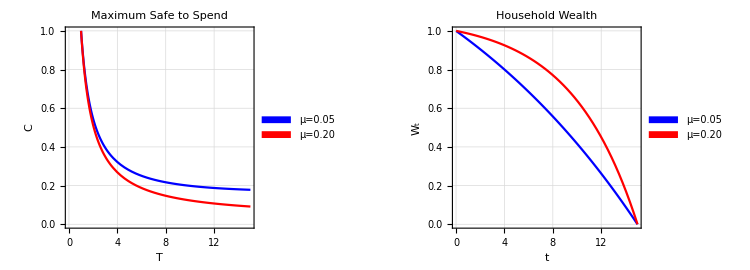

```mathematica
householdConsumption= Plot[{maxC[0.20,T],maxC[0.05,T]},{T,0.01,15},
PlotStyle->{Blue,Red,Green},
PlotLabel->"Maximum Safe to Spend",
PlotLegends->Placed[SwatchLegend[{"μ=0.05","μ=0.20"}],{0.87,0.88}],
FrameLabel->{"T","C"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0,15},{0,1}}];
householdWealth= Plot[{w[0.05,t,15],w[0.20,t,15]},{t,0.01,15},
PlotStyle->{Blue,Red},
PlotLabel->"Household Wealth",
PlotLegends->Placed[SwatchLegend[{"μ=0.05","μ=0.20"}],{0.87,0.88}],
FrameLabel->{"t","W_t"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0,15},{0,1}}];
householdWealth=GraphicsGrid[{{householdConsumption,householdWealth}},ImageSize->{750,270}]
Export["images/household-wealth.jpeg",householdWealth];
```

## Optimal Consumption-Savings